```mathematica
(* Задача 1 *)
(* Ако вземем проекцията на F по направлението на кривата, то тя е в същата посока като нейната насоченост навсякъде => F.dr>0 навсякъде => ∫_C F.dr>0 *)
```

```mathematica
(* Задача 2 *)
F[x_,y_]:={2 y-x^2,7x+y}
(* Малката окръжност е насочена в положителна посока, а голямата в отрицателна *)
rotSgnSmall=1;
rotSgnLarge=-1;
(* Използваме 2D теорема на стокс, т.к dr={dx,dy} получаваме *)
smallInt=rotSgnSmall Integrate[∇_{x,y} ×F[x,y],{x,0,1},{y,-√(1-x^2),√(1-x^2)}];
largeInt=rotSgnLarge Integrate[∇_{x,y} ×F[x,y],{x,0,3},{y,-√(9-x^2),√(9-x^2)}];
smallInt+largeInt
```

-20 π

```mathematica
(* Задача 3 - разписано на лист защо взимаме това F *)
F[t_]:={-y[t],x[t]}
x[t_]:=t
y[t_]:=0
lower = 0.5 Integrate[F[t].{x'[t],y'[t]},{t,0,2}];
x[t_]:=2+t
y[t_]:=2/3 t
right = 0.5 Integrate[F[t].{x'[t],y'[t]},{t,0,3}];
x[t_]:=5-t
y[t_]:=2-2/5 t
left = 0.5 Integrate[F[t].{x'[t],y'[t]},{t,0,5}];
lower+left+right
(* Веднага може да сметнем по училищната формула S=1/2.2.2 => проверка *)
lower+left+right == 1/2 2 2
```

2.

True

```mathematica
(* Задача 4 *)
(* За да не зависи от избора на крива, то полето трябва да е потенциално *)
Clear[x,y]
(* Полето *)
G={2x Exp[-y],2y - x^2 Exp[-y]};
(* Изглежда това да е потенциалът на F *)
Φ=x^2 Exp[-y]+y^2;
(* И наистина е така *)
∇_{x,y} Φ ==G
```

True

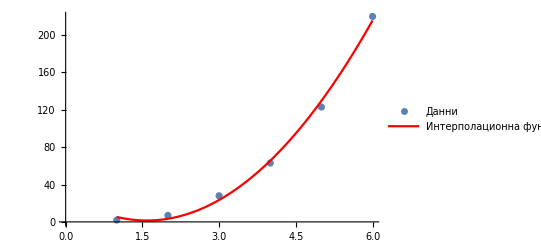

```mathematica
(* Задача 5 *)
data={
{1,2},
{2,7},
{3,28},
{4,63},
{5,123},
{6,220}
};
dataPlot=ListPlot[data,PlotLegends->{"Данни"}];
(* Изглежда парабола приближава данните *)
polyDeg=2;
generalBasis[n_]:=Table[With[{i=i},#^i&],{i,0,n}]
polyBasis=generalBasis[2];

(* Стандартно намиране на A и А^Т (тук е Subscript[A, T] заради Mathematica) *)
A=Table[Through[polyBasis[data⟦i,1⟧]],{i,1,Length@data}];
Subscript[A, T]=Transpose@A;
yList = Table[data⟦i,2⟧,{i,1,Length@data}];

(* А^Т Aq=А^Т b *)
q=LinearSolve[Subscript[A, T].A,Subscript[A, T].yList];
(* Това е интерполацията, но Mathematica не дава директно с нея  
interpolation[t_]:=q.Through@polyBasis[t] *) 
xList=Table[data⟦i,1⟧,{i,1,Length@data}];
Show[{
dataPlot,
Plot[q.Through[polyBasis[t]],{t,Min@xList,Max@xList},PlotStyle->Red,PlotLegends->{"Интерполационна функция"}]}
]
```

```mathematica
(* Задача 6 - на листа, тук проверка на сметки *)
B={{1,1,1,1},{2,3,5,6},{3,1,5,6}};
NullSpace[B]
```

{{2,1,-11,8}}

```mathematica
(* Задача 7 *) 
(* а) е вярно, т.к. Аx e линейна комбинация на сълбовете на А. Оттам ако b не е от пространството по стълбове на А, то няма как да намерим такова x. В обратна посока, b е в пространството само е от линейната обвивка на колоните на A, но тогава могат да се намерят такива коефициенти, които ако групираме във вектор, ще получим решение на системата. *)
(* б) е вярно, т.к. всеки ред от BА e линейна комбинация на редове на А. Но ако множество вектори са линейно зависими, то и всяка тяхна линейна комбинация би била. *)
```

```mathematica
(* Задача 8 *)
(* => Нека x,y са 2 решения на системата. Тогава A(x-y)=Ax-Ay=b-b=0, т.е. x-y ∈ N(A), т.е. x = y + Subscript[x, N], за някой Subscript[x, N]∈ N(A). *)
(* <= Нека Subscript[x, P] e т.ч. Subscript[Аx, P]=b и Subscript[x, N]∈ N(A). Тогава A(Subscript[x, P]+Subscript[x, N])=Subscript[Ax, P]+Subscript[Ax, N]=b+0=b, т.е Subscript[x, P]+Subscript[x, N] също е решение на системата *)
```

```mathematica
(* Задача 9 *)
Clear[x];
basis=Table[x^k,{k,0,2}];
Ttrans=CoefficientList[Integrate[#,x],x,4]&/@basis;
Subscript[T, standard]=Transpose@Ttrans;
(* матрицата на T за двата стандартни базиса *)
Subscript[T, standard] // MatrixForm
(* матрицата, която представя новите координати чрез старите *)
M={
{1,0,0,1},
{0,1,1,0},
{0,0,1,-1},
{0,0,0,1}
};
M // MatrixForm
(* T връща координати в стандартния базис, откъдето трябва тях да превърнем в координати от новия базис, т.е. ще ни трябва обратната на M и ще я умножим с "изхода" на Т, т.е. отляво *)
Subscript[T, new]=Inverse@M.Subscript[T, standard];
Subscript[T, new] // MatrixForm
```

(0 | 0 | 0
1 | 0 | 0
0 | 1/2 | 0
0 | 0 | 1/3)

(1 | 0 | 0 | 1
0 | 1 | 1 | 0
0 | 0 | 1 | -1
0 | 0 | 0 | 1)

(0 | 0 | -1/3
1 | -1/2 | -1/3
0 | 1/2 | 1/3
0 | 0 | 1/3)

```mathematica
(* Задача 10 - на листа *)
```